```mathematica
Get[StringJoin[NotebookDirectory[],"PlaneCurvePlot.wl"]]
```

## Conchoid

#### Conchoid of Nicomedes

```mathematica
PlaneCurvePlot[{x,1},{x,-3,3,.2},ConchoidSetting->{{0,0},{-2,2,1}},DotStyle->{Hue[0],Hue[.7],Hue[.8]},PlotDot->False]
```

-Graphics-

#### Limacon of Pascal

```mathematica
PlaneCurvePlot[{Sin[x],Cos[x]},{x,0,2 π,(2 π)/30},ConchoidSetting->{{0,-1},{-1,1}},PlotDot->False,PlotRange->{{-2,2},{-1.3,2.2}}]
```

-Graphics-

#### (* Conchoid of Sinusoid *)

```mathematica
PlaneCurvePlot[{x,Sin[x]},{x,0,10,0.25},ConchoidSetting->{{2,0},{-2,0,2}},PlotDot->False,DotStyle->{Hue[0],Hue[0.7],Hue[0.8]},PlotRange->{{-1,12},{-2,3}}]
```

-Graphics-

```mathematica
PlaneCurvePlot[{(3 Cos[t])/5+0.13 Cos[(3 t)/2],(3 Sin[t])/5-0.13 Sin[(3 t)/2]},{t,0,2 2 π,(2 2 π)/(5 20)},ConchoidSetting->{{0,0},{-.2,1}},Axes->False,PlotDot->False]
```

-Graphics-

#### (* Conchoid of an epitrochoid with parameter {1, 1/5, 2} *)

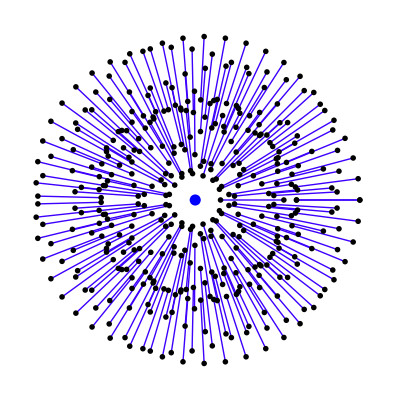

```mathematica
PlaneCurvePlot[{(6 Cos[t])/5+2 Cos[6 t],(6 Sin[t])/5+2 Sin[6 t]},{t,0,2 π,(2 π)/(5 40)},ConchoidSetting->{{0,0},{0,2}},Axes->False,PlotDot->False,PlotCurve->False,LineStyle->{{Hue[Random[]]}},DotStyle->{PointSize[.01]}]
```